Autor: Paweł Zapiór

# Metody numeryczne (Informatyka)

## Projekt 6

Aproksymacja średniokwadratowa dyskretna

Napisać procedurę realizującą algorytm aproksymacji średniokwadratowej dyskretnej. 
Działanie procedury przetestować na przykładzie z wykładu.

a) Aproksymować punkty (x_i, cos x_i) dla x_i=-6,-5,...,5,6, wielomianem stopnia czwartego. Jako funkcję wagową raz przyjąć funkcję w(x)=1, natomiast drugi raz funkcję w(x)={10 | dla |x|≤2,
10^-10 | dla |x|>2.
Wykreślić na wspólnym rysunku otrzymane wielomiany oraz punkty aproksymacji.

b) Zmianę temperatury płynu w zbiorniku ilustruje następująca tabela:

t[s] | 0 | 60 | 120 | 180 | 240 | 300
T[°C] | 100 | 90 | 80 | 72 | 65 | 58

Aproksymować temperaturę funkcją postaci T(t)=a exp(b  t). Jako funkcję wagową przyjąć w(t)=1. Policzyć temperaturę płynu po 200 s od chwili początkowej.

## Rozwiązanie

### Program

```mathematica
ClearAll["Global`*"];
```

```mathematica
φ[0][x_]:=1;
φ[i_][x_]:=x^i;
(*φ - funkcja bazowa, n-stopień wielomianu*)
```

```mathematica
aproksymacja [φ_,xa_,ya_,st_,w_]:=Module [{f,n,l,d,i,j,k,a,F},

n=st+1;
l=Length[xa];
f=Table[0,{n}];
For[k=1,k≤n,k++,

f[[k]]=∑_(j=1)^l (w[xa[[j]]]*ya[[j]]*φ[(k-1)][xa[[j]]]);
];

d=Table[0,{n},{n}];
For[i=1,i≤n,i++,
For[k=1,k≤n,k++,
d[[i,k]]=∑_(j=1)^l (w[xa[[j]]]*φ[i-1][xa[[j]]]*φ[k-1][xa[[j]]]);
];
];
a=LinearSolve[d,f];

F=0;
For[i=1,i≤Length[a],i++,
F=F+a[[i]]*φ[i-1][x];
];
Simplify[F];
Print[F];
Return[F];
]
```

### Przykład testowy

```mathematica
x1={0,1,2,3};
y1={1,-1,2,4};
w[x_]:=1;
aproksymacja[φ,x1,y1,2,w]
```

7/10-(9 x)/5+x^2

7/10-(9 x)/5+x^2

### Zadanie a)

```mathematica
w1[x_]:=1;
```

```mathematica
xa={-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6};
```

```mathematica
ya={Cos[xa[[1]]],Cos[xa[[2]]],Cos[xa[[3]]],Cos[xa[[4]]],Cos[xa[[5]]],Cos[xa[[6]]],Cos[xa[[7]]],Cos[xa[[8]]],Cos[xa[[9]]],Cos[xa[[10]]],Cos[xa[[11]]],Cos[xa[[12]]],Cos[xa[[13]]]};
Zad1a=aproksymacja[φ,xa,ya,4,w1]//N
```

(x^2 (-1890-3016 Cos[1]-971 Cos[2]+1614 Cos[3]+3504 Cos[4]+2970 Cos[5]-2211 Cos[6]))/58344+(x^4 (42+64 Cos[1]+11 Cos[2]-54 Cos[3]-96 Cos[4]-66 Cos[5]+99 Cos[6]))/58344+(677+1200 Cos[1]+780 Cos[2]+220 Cos[3]-270 Cos[4]-396 Cos[5]+220 Cos[6])/2431

0.43536-0.141988 x^2+0.00453425 x^4

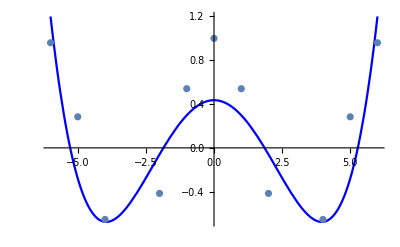

```mathematica
Print[Show[Plot[Zad1a,{x,xa[[1]],xa[[Length[xa]]]},PlotStyle->Blue], ListPlot[Thread[{xa,ya}]]]];
```

```mathematica
Clear[w2];
w2[x_]:=10/;Abs[x]<2;
w2[x_]:=10^-10
```

```mathematica
Zad1b=aproksymacja[φ,xa,ya,4,w2]//N
```

1/418860001948034400007593144 x^2 (-431925000083518500000000000+432379999855507600000000000 Cos[1]-2499961709100000834181 Cos[2]-14999921496600000034926 Cos[3]-49999899637699999375134 Cos[4]-124999930570999999313970 Cos[5]-262500058574700000441789 Cos[6])+(1342500002406850000000000+4290000000000000 Cos[1]-70499999971410 Cos[2]-154499999990590 Cos[3]-201750000007635 Cos[4]-141900000012738 Cos[5]+115500000006710 Cos[6])/1342500006243700000024337+1/418860001948034400007593144 x^4 (13065000001821300000000000-13519999996890400000000000 Cos[1]+2499998837100000016741 Cos[2]+14999997663599999998266 Cos[3]+49999997153299999983846 Cos[4]+124999998438799999984926 Cos[5]+262500002976300000016221 Cos[6])

1.-0.47402 x^2+0.0143223 x^4

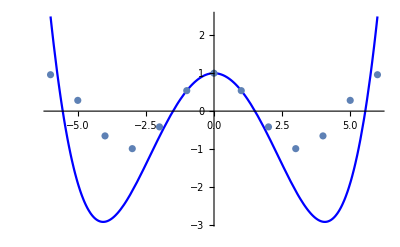

```mathematica
Print[Show[Plot[Zad1b,{x,xa[[1]],xa[[Length[xa]]]},PlotStyle->Blue], ListPlot[Thread[{xa,ya}]]]];
```

### Zadanie b)

T(t) = a exp (b t)  /ln()
ln T(t) = ln(a exp(b t))
ln T(t) = ln a +  b t
y=c + bx
//gdzie y = lnT[t], c= lna,

```mathematica
t={0,60,120,180,240,300};
```

```mathematica
T={100,90,80,72,65,58};
```

```mathematica
w1[x_]:=1;
```

```mathematica
dane=Transpose[{t,T}]
```

{{0,100},{60,90},{120,80},{180,72},{240,65},{300,58}}

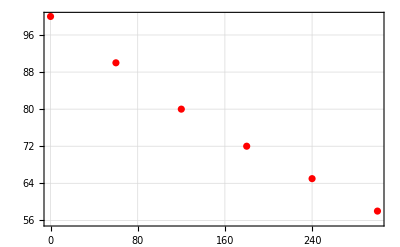

```mathematica
p1=ListPlot[{dane},PlotStyle->{Red,PointSize[0.015]},PlotTheme->"Detailed"]
```

```mathematica
logT=Log[T]
```

{Log[100],Log[90],Log[80],Log[72],Log[65],Log[58]}

```mathematica
Zad2=aproksymacja[φ,t,logT,1,w2]//N
```

(x (33333333334 Log[58]+26666666667 Log[65]+20000000000 Log[72]+13333333333 Log[80]+6666666666 Log[90]-100000000000 Log[100]))/22000000000200+(-4 Log[58]-Log[65]+2 Log[72]+5 Log[80]+8 Log[90]+1100000000000 Log[100])/1100000000010

4.60517-0.00181331 x

```mathematica
c=4.605170185988086;
```

```mathematica
b=-0.0018133113214486253;
```

```mathematica
a=Exp[c];
```

```mathematica
fun[xn_]:=a Exp[b*xn]
```

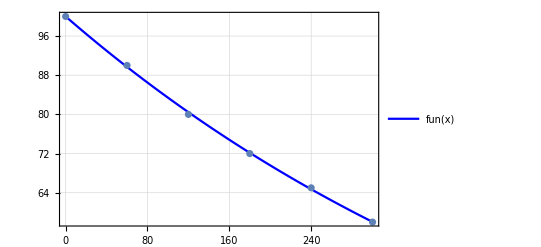

```mathematica
Show[Plot[fun[x],{x,t[[1]],t[[Length[t]]]},PlotStyle->Blue,PlotTheme->"Detailed"],ListPlot[Thread[{t,T}]]]
```

```mathematica
fun[200]
```

69.5821

Odp. Po 20 s temperatura wynosiła 69.5821 stopnia Celsjusza.